```mathematica
SetDirectory[NotebookDirectory[]];
```

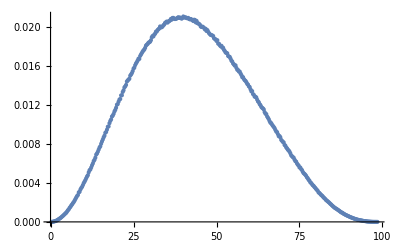

```mathematica
data=Import["MC_pddf_alpha-spheres_alpha_REG2=1.dat"];
ListPlot[data]
```

InterpolatingFunction::dmval: Input value {0.00201226} lies outside the range of data in the interpolating function. Extrapolation will be used.

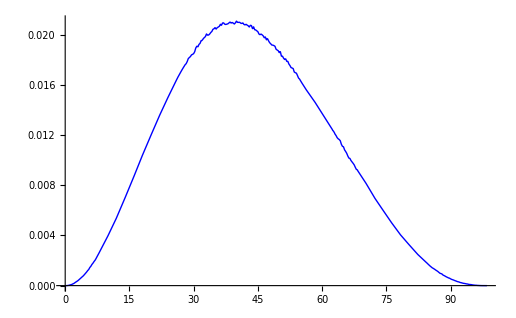

```mathematica
datainterp=Interpolation[data,InterpolationOrder->1];plotinterp=Plot[datainterp[r],{r,Min[data],Max[data]},PlotStyle->{Blue,Thick}]
```

```mathematica
Rg=(NIntegrate[r^2 datainterp[r],{r,0,100}]/2)^(1/2)
```

32.9922

```mathematica
(*The correction for alpha-shape is 2%*)
```

```mathematica
Rgfin=Rg+0.02 Rg
```

33.652

```mathematica
26 26
```

676